```mathematica
F1[f_, n_,1] := If[ n <2, 0, f[n]]
```

```mathematica
F1[MoebiusMu, 1, 1]
```

0

```mathematica
pf[f_,x_]:=f[x]+f[1-x]
```

```mathematica
pf[MoebiusMu, 3]
```

-2

```mathematica
abs[f_, x_]:=If[x<0,-f[x],f[x]]
```

```mathematica
abs[MoebiusMu, 3]
```

Set::setraw: Cannot assign to raw object 3.

If[0,-MoebiusMu[3],MoebiusMu[3]]

```mathematica
F1[f_, n_,0] := If[ n <2, 1, 0]
```

```mathematica
F1[f_,n_,1]:=If[n<2,0,f[n]]
```

```mathematica
F1[f_, n_, k_] := Sum[F1[ f, d, 1] F1[ f, n/d, k-1],{d,Divisors[n]}]
```

```mathematica
F1[MoebiusMu, 30, 3]
```

-6

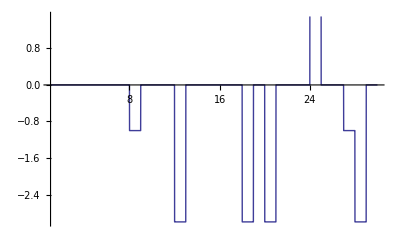

```mathematica
Plot[ F1[MoebiusMu, Floor[n], 3], {n,1,30}]
```

```mathematica
F2[ f_, n_, k_ ] := Sum[ F1[f,j,k], {j,2,n}]
```

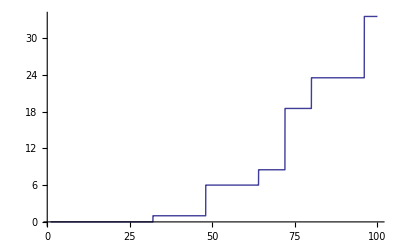

```mathematica
DD[n_] := 1
PP[n_] := FullSimplify[ MangoldtLambda[ n] / Log[n] ]
Plot[ F2[PP, Floor[n], 5], {n,1,100}]
```